```mathematica
Unprotect[npredictors];
SetDirectory[NotebookDirectory[]];
<<EQLab2`
```

```mathematica
(*measurements*)
ProbabilityPlus=0.5;
UserMeasure[]:=RandomReal[]//Which[#<ProbabilityPlus,1,True,-1]&(*simple yes or no answer with equal probability*)
(*forecasts*)
predictivepower2[xrandom_,meas_]:=Which[meas==1,1-xrandom^6,meas==-1,xrandom^6]
predictivepower1[xrandom_,meas_]:=Which[meas==1,1-xrandom^2,meas==-1,xrandom^2]
predictivepower0[xrandom_,meas_]:=Which[meas==1,1-xrandom,meas==-1,xrandom]
predictivepowerm1[xrandom_,meas_]:=Which[meas==1,xrandom^(2) ,meas==-1,1-xrandom^(2) ]
predictivepowerm2[xrandom_,meas_]:=Which[meas==1,xrandom^(6) ,meas==-1,1-xrandom^(6) ]

predictivepower[xrandom_,meas_,g_]:=Which[(*should correspond to p(ν,di) in Eq 17*)
g==2,predictivepower2[xrandom,meas],
g==1,predictivepower1[xrandom,meas],
g==0,predictivepower0[xrandom,meas],
g==-1,predictivepowerm1[xrandom,meas],
g==-2,predictivepowerm2[xrandom,meas]
]

INITIALbeliefinα={(*d_i in Eq 15. This array gets updated*)
2,  (*player A*)
1,  (*player B*)
0,   (*player C*)
-1,(*player D*)
-2    (*player E*)
};
beliefinα={};
COPIES=2;
For[i=1,i≤COPIES,i++,
AppendTo[beliefinα,INITIALbeliefinα]
]
beliefinα=beliefinα//Flatten;

affinity=ConstantArray[0,(INITIALbeliefinα//Length)*COPIES];

randomwalkprob=ConstantArray[0.99,(INITIALbeliefinα//Length)*COPIES];


PredictivePower=Table["<|
\"A"<>ToString[i]<>"\"→(predictivepower[#1,#2,beliefinα[[1]]]&),
\"B"<>ToString[i]<>"\"→(predictivepower[#1,#2,beliefinα[[2]]]&),
\"C"<>ToString[i]<>"\"→(predictivepower[#1,#2,beliefinα[[3]]]&),
\"D"<>ToString[i]<>"\"→(predictivepower[#1,#2,beliefinα[[4]]]&),
\"E"<>ToString[i]<>"\"→(predictivepower[#1,#2,beliefinα[[5]]]&)
|>",{i,1,COPIES}]//ToExpression//Apply[Join];
 

npredictors=PredictivePower//Length



BeliefCurrent={};
BELIEF={};

(*Random walk update of belief according to draft*)
RandomWalk[]:=Module[
{rewards,maxreward,avgrewards,leadingexpert,stepplus={},stepminus={}},
rewards=CREWARD[[-1,All,-1]];
maxreward=Max[rewards];
avgrewards=Mean[rewards];
leadingexpert=Position[rewards,maxreward]//Flatten//Part[#,1]&;

stepplus=Table[
Which[(*if ν1<h, proceed with random walk upwards*)
Random[]<=randomwalkprob[[i]],1,
True,0
],
{i,1,beliefinα//Length}];

stepminus=Table[
Which[(*if ν2<h, proceed with random walk downwards*)
Random[]<=randomwalkprob[[i]],-1,
True,0
],
{i,1,beliefinα//Length}];


(*update d_i according to random walk*)
beliefinα=beliefinα+stepplus+stepminus;


(*make sure that  -2 ≤ d_i ≤ 2, if not, force out of bounds values to wither +1 or -1*)
beliefinα=Table[
Which[
(beliefinα[[i]]<-2),beliefinα[[i]]=-1,
(beliefinα[[i]]>  2),beliefinα[[i]]=   1,
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];

]

UpdateBelieveinαAffinity[]:=Module[
{rewards,maxreward,avgrewards,Largerewards,leadingexpert,changebelief={},beliefinαTEMP,it},
rewards=CREWARD[[-1,All,-1]];
maxreward=Max[rewards];
avgrewards=Mean[rewards];
Largerewards=(maxreward+avgrewards)/2;

leadingexpert=Position[rewards,maxreward]//Flatten//Part[#,1]&;


changebelief=Table[
TrueQ[
!(Random[]<Exp[- affinity[[i]](1-rewards[[i]]/Largerewards)])
]
,{i,1,beliefinα//Length}];

(*For[it=1,it≤(beliefinα//Length),it++,
Print[it,") P of changing belief = ",1-Exp[- affinity[[it]](1-rewards[[it]]/Largerewards)] ]
];*)

beliefinα=Table[
Which[
changebelief[[i]],beliefinα[[i]]+Sign[  beliefinα[[leadingexpert]]-beliefinα[[i]]  ],
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];
(*AppendTo[BeliefCurrent,beliefinα];*)

];

UpdateBelieveinα[]:=Module[
{},
RandomWalk[];
UpdateBelieveinαAffinity[];
AppendTo[BeliefCurrent,beliefinα];
]


PrintBelieveinα[]:=Module[
{names=PLOTLEGENDS[[1,1;;npredictors]],output},
output=Table[names[[i]]<>"->"<>ToString[beliefinα[[i]]]<>"\n",{i,1,npredictors}]//StringJoin;
Print[Style["------ Current belief in theory α ---------",Red,Large]];
Print[Style["after ",Bold,Large],Style[BeliefCurrent//Length,Bold,Large,Blue],Style[" questions.",Bold,Large]];
Print[Style[output,Blue,Large]]
]


UserPredict[exp_,newquestion_]:=Module[
{forecasts={},tags},
tags=Table[(#<>ToString[i])&/@{"A","B","C","D","E"},{i,1,COPIES}]//Flatten;
Which[
(exp//Length)>1,UpdateBelieveinα[];,
True,Nothing
];
forecasts=Table[RandomReal[{0.001,0.999}]//PredictivePower[i][#,newquestion[[2]]]&,{i,tags}];
forecasts
]


(*resolutions*)

(*plays the role of 'b' in Eq 19 in draft *)

bias=ConstantArray[0,5*COPIES];

UserResolve[exp_,newquestion_]:=Module[
{objectiveSij,objectiveSjavg,resolutions,wj,i},
objectiveSij=ObjectiveSurprisal[newquestion];
objectiveSjavg=Mean[objectiveSij];
wj=newquestion[[2]];

resolutions=Table[
Which[
Random[]<Exp[-bias[[i]]*(objectiveSij[[i]]/objectiveSjavg-1)] , wj,
True,-wj
],
{i,1,newquestion[[1]]//Length}
]

]

(*condition to stop simulation*)
UserStop[]:=((beliefinα//DeleteDuplicates//Length)==1)(*&&Length[BeliefCurrent]>100*);

(*load user function into EQLab*)
SetUserFunctions[]
nquestions=5000;

initsimulation[]:=Module[
{},
beliefinα={};
For[i=1,i≤COPIES,i++,
AppendTo[beliefinα,INITIALbeliefinα]
];
beliefinα=beliefinα//Flatten;
BeliefCurrent={};
AppendTo[BeliefCurrent,beliefinα]
]

StoreBeliefCurrent[]:=AppendTo[BELIEF,BeliefCurrent];

(*overrides legends in EQLab*)
PLOTLEGENDS=Table[#<>ToString[i]&/@{
"expert A","expert B","expert C","expert D","expert E"
},{i,1,COPIES}]//Flatten//Placed[#,Above]&;

outputsimulation[expi_,questioni_,append_:False]:=Module[
{},
If[append,StoreBeliefCurrent[],Nothing,Nothing];
PrintBelieveinα[];
markerlist=marker2[White,#1,#2]&@@@(ColorData[97,"ColorList"]//Table[{#[[i]],50-i*7},{i,1,npredictors}]&);
plotbelief=BELIEF[[expi,questioni]]//Transpose//ListLinePlot[#,PlotMarkers->markerlist,PlotRange->{-2.5,2.5},ImageSize->{1000,500},LabelStyle->Directive[Bold, 16],AxesOrigin->{-(Length[#[[1]]]*0.05),-2.5},AxesLabel->{Style["j",Bold,Large],Style["d_i(j)",Bold,Large]},(*PlotLegends->PLOTLEGENDS,*)PlotStyle->Thick]&;
Print[plotbelief];

]

outputsimulation[]:=outputsimulation[-1,All,True]


(*Protect[npredictors];*)(*this simulation is written for 5 players only.*)
```

10

```mathematica
outputsimulation[expi_,questioni_,append_:False]:=Module[
{},
If[append,StoreBeliefCurrent[],Nothing,Nothing];
PrintBelieveinα[];
markerlist=marker2[White,#1,#2]&@@@(ColorData[97,"ColorList"]//Table[{#[[i]],50-i*7},{i,1,npredictors}]&);
plotbelief=BELIEF[[expi,questioni]]//Transpose//ListLinePlot[#,PlotMarkers->markerlist,PlotRange->{-2.5,2.5},ImageSize->{1000,500},LabelStyle->Directive[Bold, 16],AxesOrigin->{-(Length[#[[1]]]*0.05),-2.5},AxesLabel->{Style["j",Bold,Large],Style["d_i(j)",Bold,Large]},PlotLegends->PLOTLEGENDS,PlotStyle->Thick]&;
Print[plotbelief];

]
outputsimulation[-1,All,False]
```

```mathematica
outputsimulation[]
```

------ Current belief in theory α ---------

after 99 questions.

expert A1->2
expert B1->1
expert C1->1
expert D1->2
expert E1->2
expert A2->2
expert B2->1
expert C2->0
expert D2->1
expert E2->0

Example 1:  Affinity and random walk already in. Simulations stop after “agreement” is reached in the degree of belief of theory α, provided at least 100 questions have been asked. Simulation stops after ‘nquestions’ has been reached, even if no agreement happened.

```mathematica
PLOTLEGENDS
```

Placed[{expert A1,expert B1,expert C1,expert D1,expert E1,expert A2,expert B2,expert C2,expert D2,expert E2},Above]

{{2,1,0,-1,-2,2,1,0,-1,-2}}

------ Current belief in theory α ---------

after 538 questions.

expert A1->2
expert B1->2
expert C1->2
expert D1->2
expert E1->2
expert A2->2
expert B2->2
expert C2->2
expert D2->2
expert E2->2

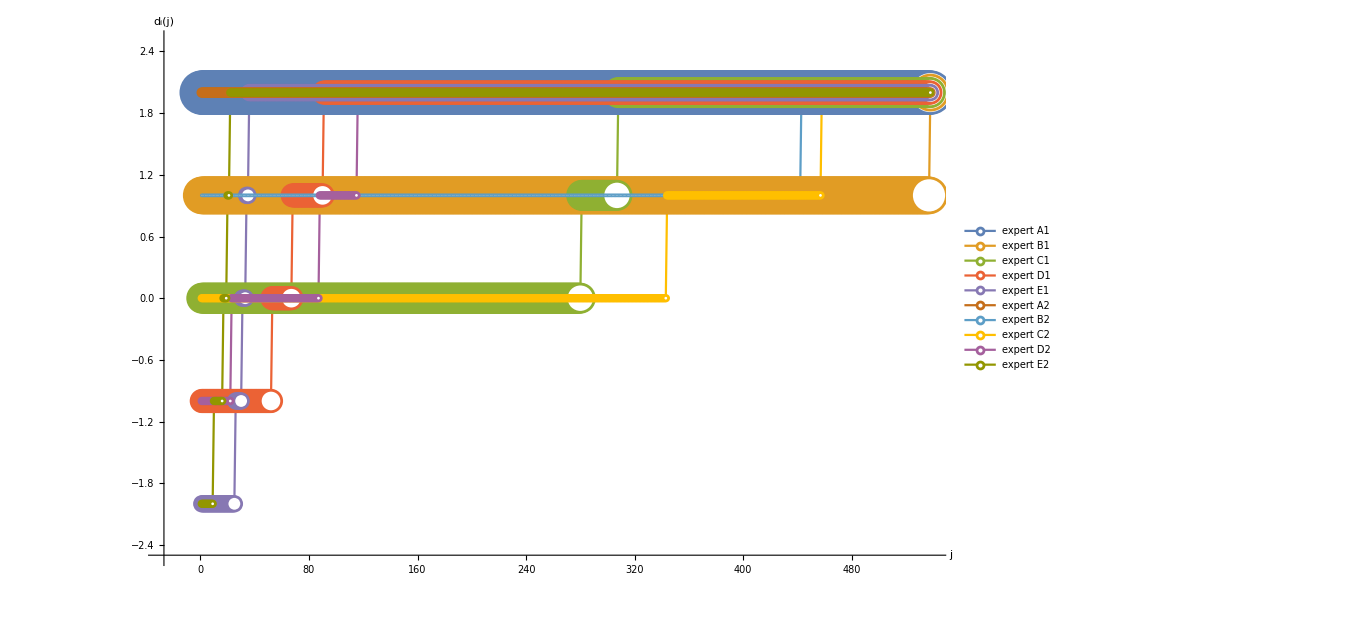

```mathematica
nquestions=1000;(*absolute max of questions asked*)
COPIES=2;

INITIALbeliefinα={
2,  (*player A*)
1,  (*player B*)
0,   (*player C*)
-1,(*player D*)
-2(*player E*)
};
randomwalkprob=ConstantArray[0,5*COPIES];

Affinity[probupdate_,δijtilde_:1]:=1/δijtilde Log[1/(1-probupdate)] (*here δijtilde=1-rij/rLargej*)
a1σ=Affinity[0.68];
a2σ=Affinity[0.954];
a3σ=Affinity[0.997];

affinity=ConstantArray[Affinity[0.1],5*COPIES];

Bias[probrejectwj_,δijtilde_:1]:=1/δijtilde Log[1/(1-probrejectwj)] (*here δijtilde=sijhat/(<sjhat>)-1  *) 
b1σ=Bias[0.68];
b2σ=Bias[0.954];
b3σ=Bias[0.997];

bias=ConstantArray[Bias[0.5],5*COPIES];

initsimulation[]
RunExperimentStop[]
outputsimulation[]
(*Print[Style["Diagram for last 20 questions:",Bold,Large]]*)
(*outputsimulation[-1,-20;;-1]*)
(*ShowPlots[-1,"rcumul"]*)
(*ShowPlots[-1,"savgj"]*)
```

```mathematica
Bias[1-0.99]
Bias[0.99]
```

0.0100503

4.60517

```mathematica
(*data=Table[predictivepower[Random[],1,2],{i,10^2}];
hist=HistogramDistribution[data];
DiscretePlot[PDF[hist,x],{x,0,1,0.001},PlotRange->All]
(data//Cases[x_/;x>0.9]//Length)/(data//Length)//N
*)
```

```mathematica
(*data=Table[predictivepower[Random[],1,1],{i,10^5}];
hist=HistogramDistribution[data];
DiscretePlot[PDF[hist,x],{x,0,1,0.001},PlotRange->All]
(data//Cases[x_/;x>0.55]//Length)/(data//Length)//N
*)
```

```mathematica
(*data=Table[predictivepower[Random[],1,0],{i,10^5}];
hist=HistogramDistribution[data];
DiscretePlot[PDF[hist,x],{x,0,1,0.001},PlotRange->All]
(data//Cases[x_/;x>0.5]//Length)/(data//Length)//N
*)
```

```mathematica
(*data=Table[predictivepower[Random[],1,-1],{i,10^5}];
hist=HistogramDistribution[data];
DiscretePlot[PDF[hist,x],{x,0,1,0.001},PlotRange->All]
(data//Cases[x_/;x<0.45]//Length)/(data//Length)//N*)
```

```mathematica
(*data=Table[predictivepower[Random[],1,-2],{i,10^5}];
hist=HistogramDistribution[data];
DiscretePlot[PDF[hist,x],{x,0,1,0.001},PlotRange->All]
(data//Cases[x_/;x<0.1]//Length)/(data//Length)//N*)
```

```mathematica
(**)
```

```mathematica
(*Table[predictivepower[x,1,i],{i,-2,2}]//Plot[#,{x,0,1},PlotLabels->{-2,-1,0,1,2}]&*)
```

```mathematica
(**)
```

```mathematica
(*Plot[Table[BernsteinBasis[x,1,i],{i,-2,2}],{x,0,1}]*)
```

```mathematica
(*Table[ShowPlots[i,"rcumul"],{i,1,EXPERIMENT//Length}]*)
```

```mathematica
(*BELIEF//Length*)
```

```mathematica
(*EXPERIMENT//Length*)
```

-1

```mathematica
nquestions=1;(*absolute max of questions asked*)
COPIES=2;
npredictors=5*COPIES;
INITIALbeliefinα={
1,  (*player A*)
0,  (*player B*)
-1,   (*player C*)
-2,(*player D*)
-2(*player E*)
};
randomwalkprob=ConstantArray[0.99,5*COPIES];

Affinity[probupdate_,δijtilde_:1]:=1/δijtilde Log[1/(1-probupdate)] (*here δijtilde=1-rij/rLargej*)
a1σ=Affinity[0.68];
a2σ=Affinity[0.954];
a3σ=Affinity[0.997];

affinity=ConstantArray[Affinity[0.1],5*COPIES];

Bias[probrejectwj_,δijtilde_:1]:=1/δijtilde Log[1/(1-probrejectwj)] (*here δijtilde=sijhat/(<sjhat>)-1  *) 
b1σ=Bias[0.68];
b2σ=Bias[0.954];
b3σ=Bias[0.997];

bias=ConstantArray[Bias[0.5],5*COPIES];


PTS=600;
biasaffpair={};
BeliefFinal={};
(*StdProbOfRejectingWjMIN=0.01;StdProbOfRejectingWjMAX=0.99;
StdProbOfChangeInBeliefMIN=0.01;StdProbOfChangeInBeliefMAX=0.99;*)
affinityMIN=0;affinityMAX=10;
biasMIN=0;biasMAX=10;
For[it=1,it≤PTS,it++,
(*StdProbOfRejectingWj=RandomReal[{StdProbOfRejectingWjMIN,StdProbOfRejectingWjMAX}];
StdProbOfChangeInBelief=RandomReal[{StdProbOfChangeInBeliefMIN,StdProbOfChangeInBeliefMAX}];*)
randomAffinity=RandomReal[{affinityMIN,affinityMAX}];
randomBias=RandomReal[{biasMIN,biasMAX}];
AppendTo[biasaffpair,{randomBias,randomAffinity}];
templine=PrintTemporary[Style["it=",Large,Bold],Style[it,Large,Bold]];
bias=ConstantArray[0,npredictors];
bias[[{3,4,5,8,9,10}]]=biasaffpair[[-1,1]];
(*bias=ConstantArray[biasaffpair[[1,-1]],npredictors];*)
affinity=ConstantArray[biasaffpair[[-1,2]],npredictors];
initsimulation[];
RunExperiment[];
StoreBeliefCurrent[];
AppendTo[BeliefFinal,BELIEF[[-1,-1]]];
Unprotect[EXPERIMENT];
Unprotect[PLOTS];
Unprotect[CSURPRISAL];
Unprotect[CREWARD];
Unprotect[ASURPRISAL];
EXPERIMENT={};
PLOTS={};
CSURPRISAL={};
CREWARD={};
ASURPRISAL={};
BELIEF={};
NotebookDelete[templine];




If[
Mod[it,50]==0,
PHASE={biasaffpair,BeliefFinal};
Export["phase_try_red_q-1_1.txt",PHASE,"String"];
NotebookDelete[temp];
plot=PhasePlot[{biasaffpair,BeliefFinal},"pts = "<>ToString[it]];
temp=PrintTemporary[plot],
Nothing,Nothing
]


]
```

```mathematica
(*PhasePlot[{biasaffpair_,BeliefFinal_},label_]:=Module[
{meanconclusion,markertable},
meanconclusion=Mean/@BeliefFinal;
markertable=marker/@(meanconclusion);

(List/@biasaffpair)//ListPlot[#,PlotMarkers->markertable,PlotRange->Automatic,ImageSize->500,LabelStyle->Directive[Bold, 16],FrameLabel->{Style["b",Bold,Large],Style["a",Bold,Large]},PlotLabel->label,PlotStyle->Thick,AspectRatio->0.9,Frame->True,ImageMargins->25]&

]*)
```

```mathematica
PHASE3={biasaffpair,BeliefFinal};
Export["phase_try_red_q-5_1.txt",PHASE3,"String"]
```

phase_try_red_q-5_1.txt

```mathematica
biasaffpair//Length
BeliefFinal//Length
```

1

1

```mathematica
Clear[temp]
```

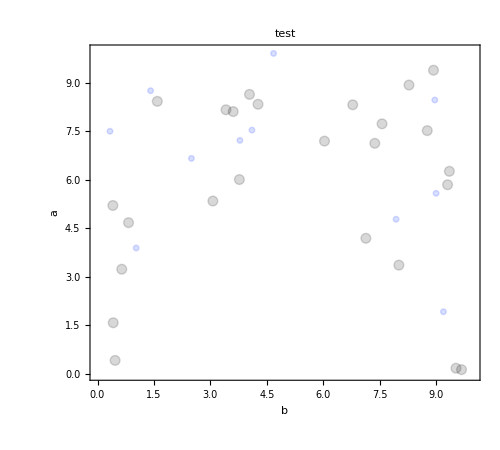

```mathematica
PhasePlot[{biasaffpair,BeliefFinal},"test"]
```

```mathematica
Mean/@(BeliefFinal)-Table[Mean[BeliefFinal[[i]]],{i,1,BeliefFinal//Length}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
BeliefFinal[[7]]
```

{2,1,0,-1,1,2,1,0,0,2}

```mathematica
Mean/@BeliefFinal
```

{2/5,1/5,2/5,2/5,1/5,3/10,4/5,0,1/5,0,1/5,2/5,1/10,1/2,3/10,3/10,2/5,2/5,0,1/10,0,1/10,3/10,1/5,1/5,1/5,2/5,1/10,1/10,3/10,1/10,3/10,0,1/5,3/10,2/5,0,1/10,1/5,1/2,1/10,2/5,0,1/5,1/5,1/5,1/5,0,1/10,3/10,1/10,1/10,1/10,1/10,1/5,1/5,1/5,1/5,3/5,0,3/5,0,0,1/10,1/5,1/10,0,3/5,1/5,3/10,1/5,2/5,0,0,2/5,3/10,1/5,1/2,1/5,1/10,1/5,1/10,1/5,3/10,1/10,1/10,3/10,2/5,2/5,3/10,0,1/2,3/10,0,3/10,3/10,1/5,2/5,1/10,0}

```mathematica
PHASE={biasaffpair,BeliefFinal};
Export["phase_6_q-5.txt",PHASE,"String"]
```

phase_6_q-5.txt

```mathematica
BeliefFinal//Length
biasaffpair//Length
```

263

264

```mathematica
(*biasaffpair=biasaffpair[[1;;-2]];*)
```

```mathematica
BeliefFinal[[1]]
```

{2,1,0,0,2,2,1,0,-1,0}

```mathematica
Mean/@BeliefFinal
```

{7/10,2/5,4/5,7/10,7/10,11/10,1,4/5,0,6/5,11/10,1/2,7/10,1/2,3/5,3/5,1,9/10,4/5,9/10,9/10,7/10,9/10,3/10,2/5,7/10,7/10,3/5,9/10,7/10,4/5,3/5,3/10,7/10,13/10,7/10,4/5,9/10,1,2/5,2/5,7/10,13/10,2/5,2/5,1/5,4/5,7/10,7/10,4/5,1/5,3/5,3/5,3/5,4/5,9/10,2/5,4/5,1,9/10,4/5,11/10,7/10,1/2,7/10,2/5,4/5,1,7/10,2/5,13/10,11/10,2/5,2/5,1/2,9/10,1,2/5,2/5,1/2,11/10,3/5,13/10,9/10,3/10,9/10,4/5,7/10,9/10,9/10,4/5,3/10,1,3/5,1/2,6/5,1,7/10,0,6/5}

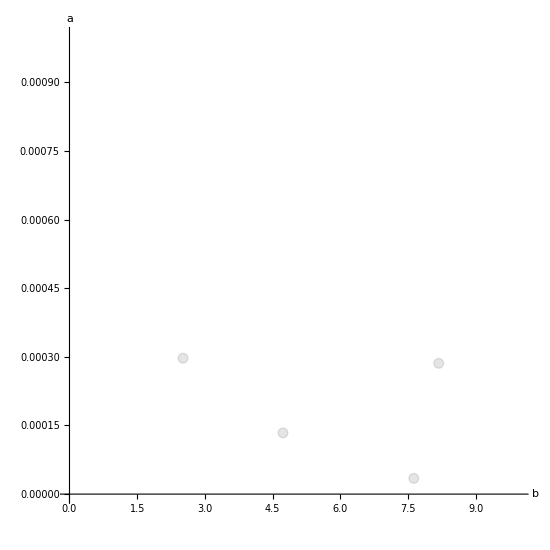

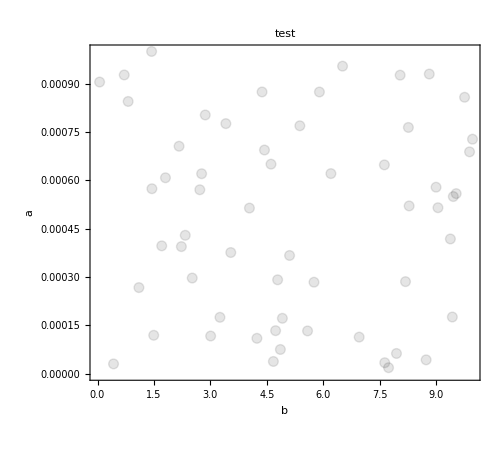

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/10,0,0,0,0,0,0,0,0,0,0,0,0,0,1/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*allagree=TrueQ[#==1]&/@Length/@DeleteDuplicates/@BeliefFinal;
conclusion={meanconclusion,allagree}//Transpose;
(*biasaffpair=List[#]&/@(Table[{biasvalues[[i]],affinityvalues[[j]]},{i,1,biasn},{j,1,affinityn}]//Flatten[#,1]&);*)
sizemarker=7;
markerphase[in_:GrayLevel[0],out_:GrayLevel[0],size_:7]:=Graphics[{in,EdgeForm[{AbsoluteThickness[1],out}],Disk[]},PlotRangePadding->0,ImageSize->size]
markerstronbelief=markerphase[ColorData["VisibleSpectrum",470],ColorData["VisibleSpectrum",470],sizemarker];
markerbelief=markerphase[White,ColorData["VisibleSpectrum",470],sizemarker];
markerneutral=markerphase[Black,Black,sizemarker];
markerdisbelief=markerphase[White,ColorData["VisibleSpectrum",630],sizemarker];
markerstrongdisbelief=markerphase[ColorData["VisibleSpectrum",630],ColorData["VisibleSpectrum",630],sizemarker];
markerNA=Style["☒",RGBColor[1, 0, 1],Large];*)

(*markeragreement[finaldofbelief_,allagree_]:=Which[
allagree&&finaldofbelief==2,markerstronbelief,
allagree&&finaldofbelief==1,markerbelief,
allagree&&finaldofbelief==0,markerneutral,
allagree&&finaldofbelief==-1,markerdisbelief,
allagree&&finaldofbelief==-2,markerstrongdisbelief,
!allagree,markerNA
]*)

(*markertable=markeragreement@@@conclusion;

phaseplot=(List/@biasaffpair)//ListPlot[#,PlotMarkers->markertable,PlotRange->Automatic,ImageSize->550,LabelStyle->Directive[Bold, 16],AxesLabel->{Style["b",Bold,Large],Style["a",Bold,Large]}(*,PlotLegends->PLOTLEGENDS*),PlotStyle->Thick,AspectRatio->1]&*)

(*phaseplot2=(List/@biasaffpair)//ListPlot[#,PlotMarkers->markertable,PlotRange->Automatic,ImageSize->550,LabelStyle->Directive[Bold, 16],AxesLabel->{Style["b",Bold,Large],Style["a",Bold,Large]}(*,PlotLegends->PLOTLEGENDS*),PlotStyle->Thick,AspectRatio->1]&*)
```

```mathematica
?Affinity
```

```mathematica
meanconclusion//N
```

{1.8,2.,1.9,2.,2.,0.5,1.7,1.7,1.9,1.8,2.,1.9,1.8,2.,0.8,1.9,2.,1.9,1.5,1.7,1.8,1.9,1.3,1.9,1.1,1.4,1.9,2.,1.8,1.4,1.9,1.7,1.9,1.9,1.9,1.9,1.7,1.9,1.7,1.8,2.,1.7,1.9,1.7,1.9,1.6,2.,1.5,1.9,0.8,1.8,1.6,2.,1.8,2.,1.7,1.8,2.,1.7,1.9,2.,1.6,1.9,1.8,2.,2.,1.6,1.,1.7,1.6,1.9,1.6,1.7,1.4,2.,1.7,1.5,1.9,1.9,1.4,2.,1.6,1.7,1.4,1.8,2.,0.7,1.6,1.7,1.9,1.8,2.,2.,1.,1.8,1.9,1.6,1.9,2.,1.8}

```mathematica
markerphase[in_:GrayLevel[0],out_:GrayLevel[0],size_:7]:=Graphics[{in,EdgeForm[{AbsoluteThickness[1],out}],Disk[]},PlotRangePadding->0,ImageSize->size]
marker[d_]:=Module[
{DMAX=2,DMIN=-2,opacity=0.08},
d//Which[
#==DMAX,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",470]],ColorData["VisibleSpectrum",470],15*Sqrt[Abs[#]]],
#==DMIN,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",630]],ColorData["VisibleSpectrum",630],15*Sqrt[Abs[#]]],
DMAX>#>0,markerphase[Transparent,ColorData["VisibleSpectrum",470],10*Sqrt[Abs[#]]],
DMIN<#<0,markerphase[Transparent,ColorData["VisibleSpectrum",630],10*Sqrt[Abs[#]]],
#==0,markerphase[Opacity[opacity,Black],Black,10],
True,Style["☒",RGBColor[1, 0, 1],Large]
]&
]


PhasePlot[{biasaffpair_,BeliefFinal_},label_]:=Module[
{meanconclusion,markertable},
meanconclusion=Mean/@BeliefFinal;
markertable=marker/@(meanconclusion);

(List/@biasaffpair)//ListPlot[#,PlotMarkers->markertable,PlotRange->Automatic,ImageSize->500,LabelStyle->Directive[Bold, 16],FrameLabel->{Style["b",Bold,Large],Style["a",Bold,Large]},PlotLabel->label,PlotStyle->Thick,AspectRatio->0.9,Frame->True,ImageMargins->25]&

]


questionsasked={1,2,3,4,5,6,10,20,100};
For[i=1,i≤(questionsasked//Length),i++,
fname="phase_try_red_q-"<>ToString[questionsasked[[i]]]<>"_1.txt";
pdfname=fname//StringReplace["txt"->"pdf"];
data=Import[fname]//ToExpression;
label="# of experts = "<>ToString[npredictors]<>"\n# of questions = "<>ToString[questionsasked[[i]]];
plot=PhasePlot[data,label](*//Print*);
Export[pdfname,plot,"PDF"]//Print
]
```

phase_try_red_q-1_1.pdf

phase_try_red_q-2_1.pdf

phase_try_red_q-3_1.pdf

phase_try_red_q-4_1.pdf

phase_try_red_q-5_1.pdf

phase_try_red_q-6_1.pdf

phase_try_red_q-10_1.pdf

phase_try_red_q-20_1.pdf

phase_try_red_q-100_1.pdf

```mathematica
INITIALbeliefinα
```

{1,0,-1,-2,-2}

```mathematica
fname="phase_try_red_q-100_1.txt";
data=Import[fname]//ToExpression//Part[#,1]&//Length
```

600

```mathematica
Export["phase_try_red_q-2_1.txt",data2,"String"];
```

```mathematica
data2=data[[All,1;;600]];
```

```mathematica
data2[[2]]//Length
```

600

```mathematica
Import["phase_q-100_1.pdf"][[1]]
```

-Graphics-

phase_q-1_1.pdf

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}